```mathematica
dir=NotebookDirectory[];
files=FileNames["Anglesnew_*.csv",dir];
```

```mathematica
process[file_]:=Module[{data,headers,tcol,acol,time,angle},data=Import[file,"CSV"];
headers=First[data];
tcol=First@FirstPosition[headers,"Time"];
acol=First@FirstPosition[headers,"Angle"];
time=data[[All,tcol]];
angle=data[[All,acol]];
Transpose@{Rest[time],(Rest[angle]-angle[[2]])*Pi/180}];
```

```mathematica
results = AssociationMap[process, files];
```

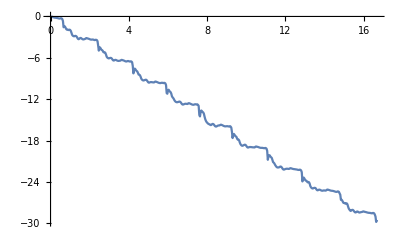
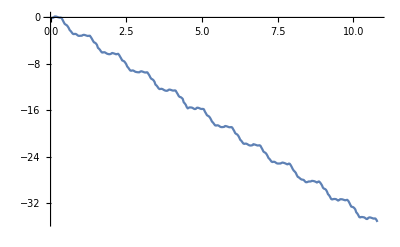
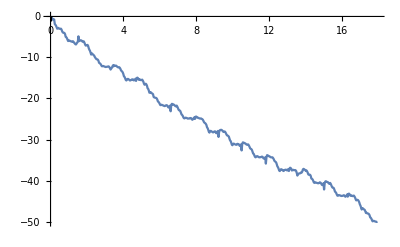
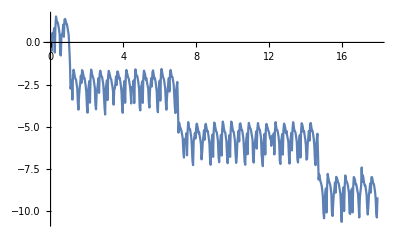
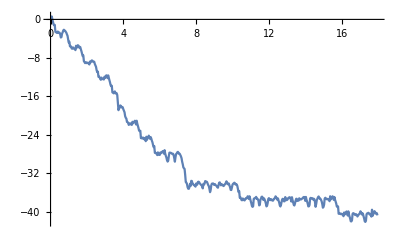
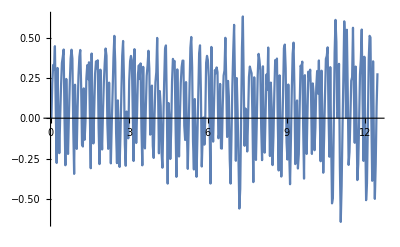

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_4cm_" <> ToString[i]<>"Hz.csv"]],{i, 1, 6}](*4 is postprocessed, there were spurious jumps. 5 is postprocessed, cut out the beginning (looks like spinning but movie doesn't) and remove spurious jumps*)
```

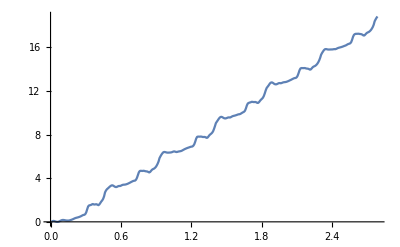
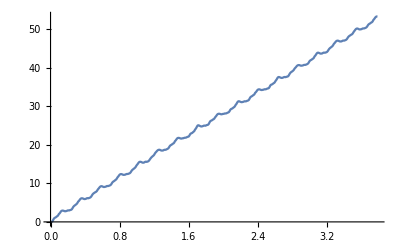
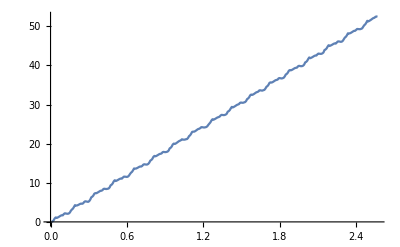
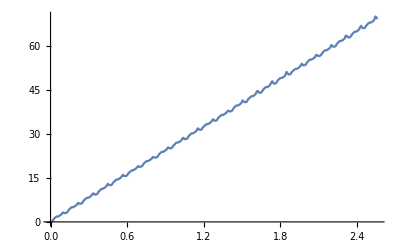
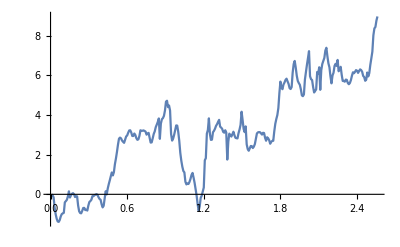
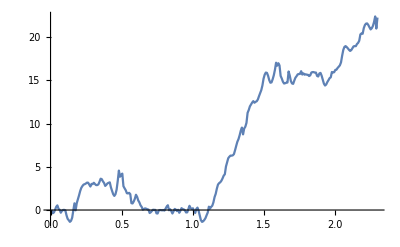

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}](*the spinning phase in 6 is almost a perfert bonnet isometry!*)
```

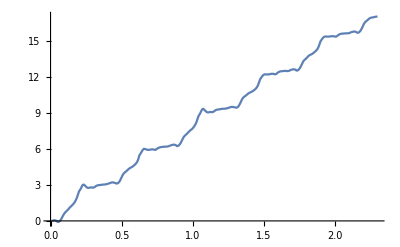
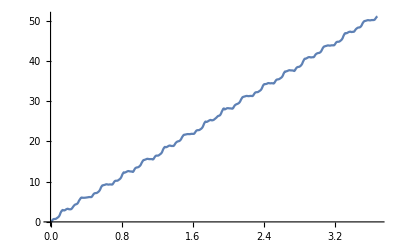
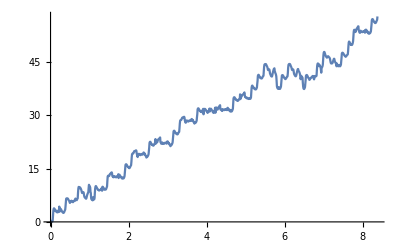
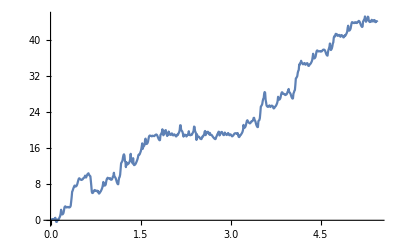
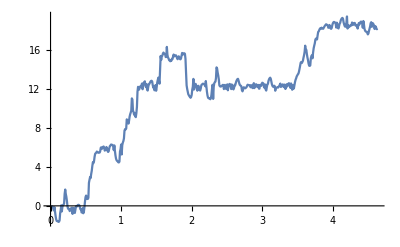
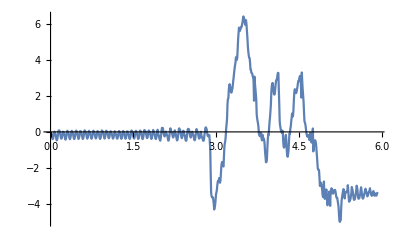

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_6cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}](*Initial dynamics of 6 is flapping*)
```

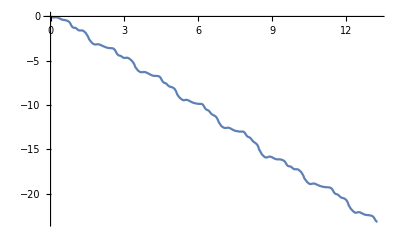
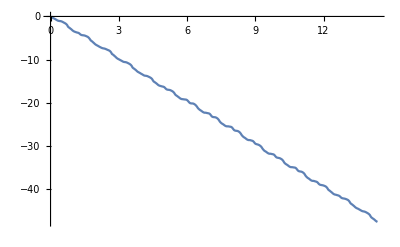
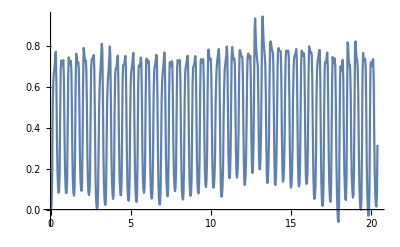
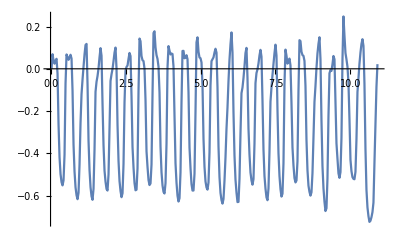
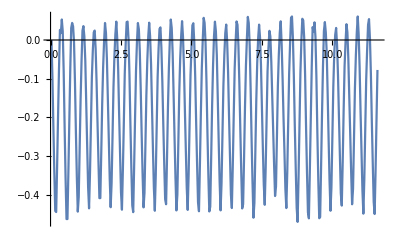
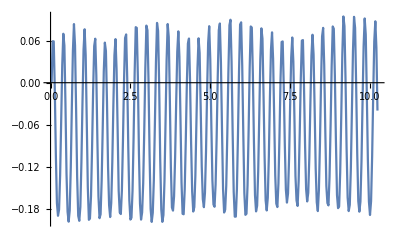

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_7cm_" <> ToString[i]<>"Hz.csv"]],{i, 1, 6}](*3 to 6 are flappings*)
```

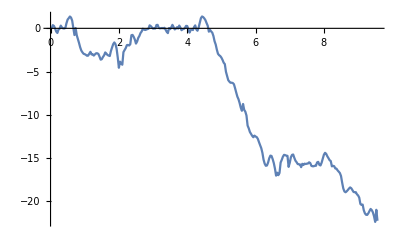
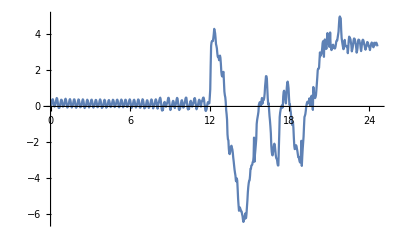
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

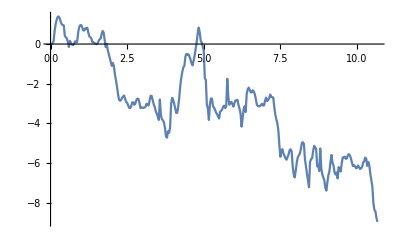
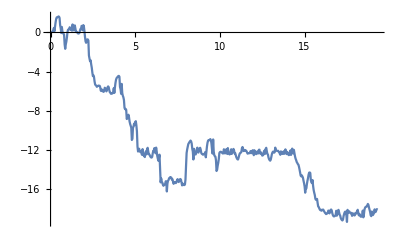
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

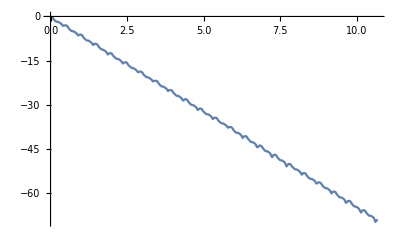
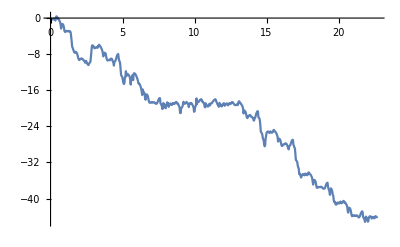
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

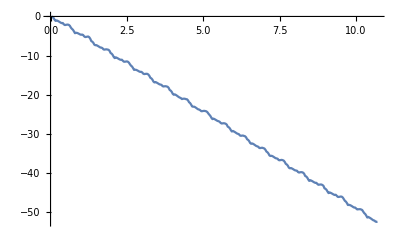
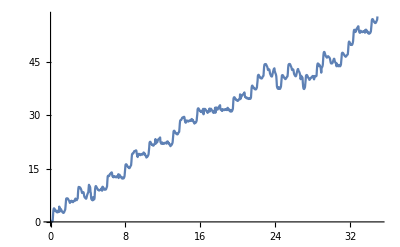
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

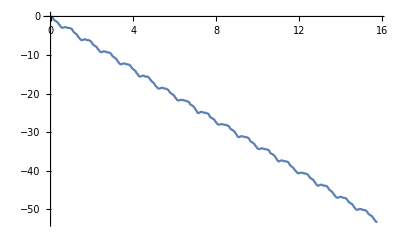
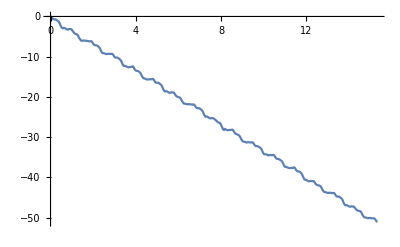
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

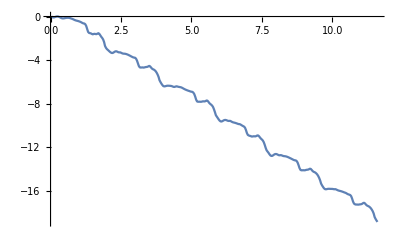
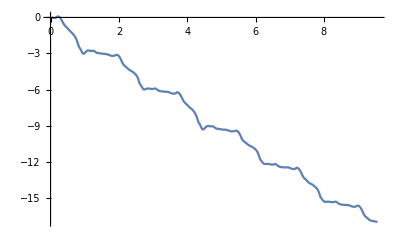
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_"<>ToString[i] <> "cm_6Hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_"<>ToString[i] <> "cm_5Hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_"<>ToString[i] <> "cm_4Hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_"<>ToString[i] <> "cm_3Hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_"<>ToString[i] <> "cm_2Hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_"<>ToString[i] <> "cm_1Hz.csv"]], {i, 4,7}]
```

## Spinning modes/Harmonic resonances

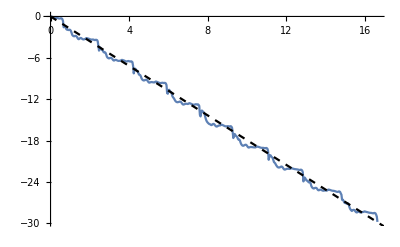
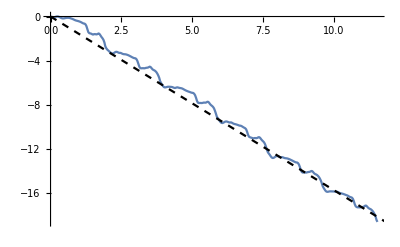
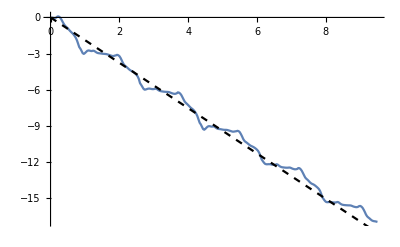
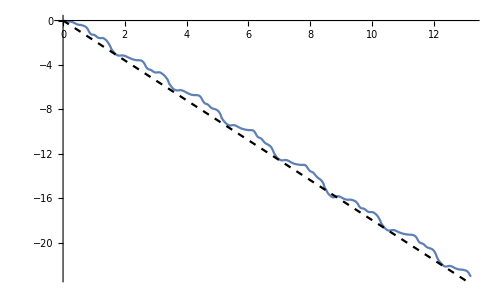

```mathematica
{Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_4cm_1Hz.csv"][[;;-3]]],
Plot[{-2Pi x (1/2)4/7}, {x, 0, 18}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]], Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_1Hz.csv"][[;;-3]]],
Plot[{-2Pi x (1/2)1/2}, {x, 0, 18}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]],Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_6cm_1Hz.csv"][[;;-3]]],
Plot[{-2Pi x (1/2)3/5}, {x, 0, 18}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]],Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_7cm_1Hz.csv"][[;;-3]]],
Plot[{-2Pi x (1/2)4/7}, {x, 0, 18}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]}
```

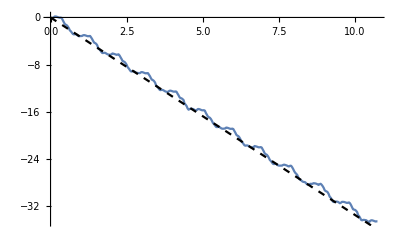
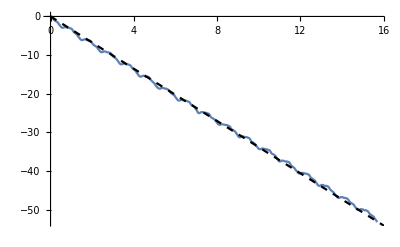
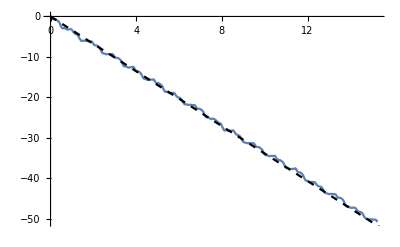
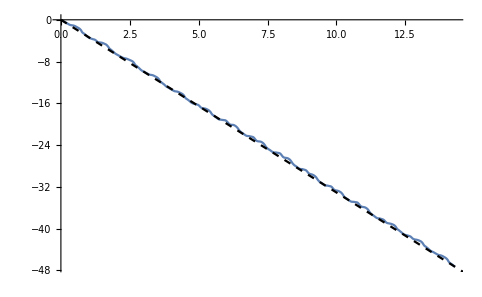

```mathematica
{Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_4cm_2Hz.csv"][[;;-3]]],
Plot[{-2Pi x (2/2)8/15}, {x, 0, 18}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]], Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_2Hz.csv"][[;;-3]]],
Plot[{-2Pi x (2/2)7/13}, {x, 0, 18}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]],Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_6cm_2Hz.csv"][[;;-3]]],
Plot[{-2Pi x (2/2)7/13}, {x, 0, 18}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]],Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_7cm_2Hz.csv"][[;;-3]]],
Plot[{-2Pi x (2/2)10/19}, {x, 0, 18}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]}
```

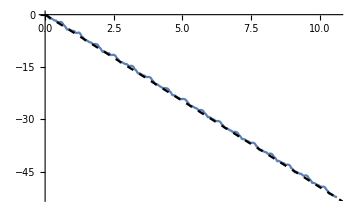

```mathematica
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_3Hz.csv"][[;;-3]]],
Plot[{-2Pi x (3/2)11/21}, {x, 0, 18}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
```

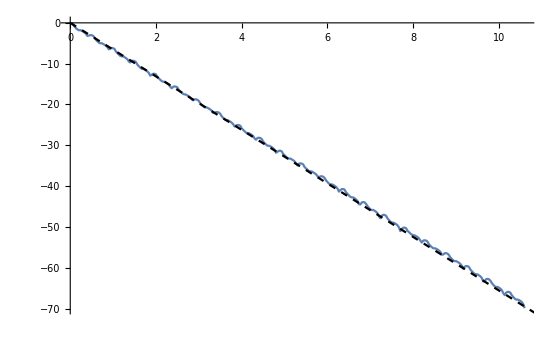

```mathematica
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_4Hz.csv"][[;;-3]]],
Plot[{-2Pi x (4/2)12/23}, {x, 0, 18}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
```

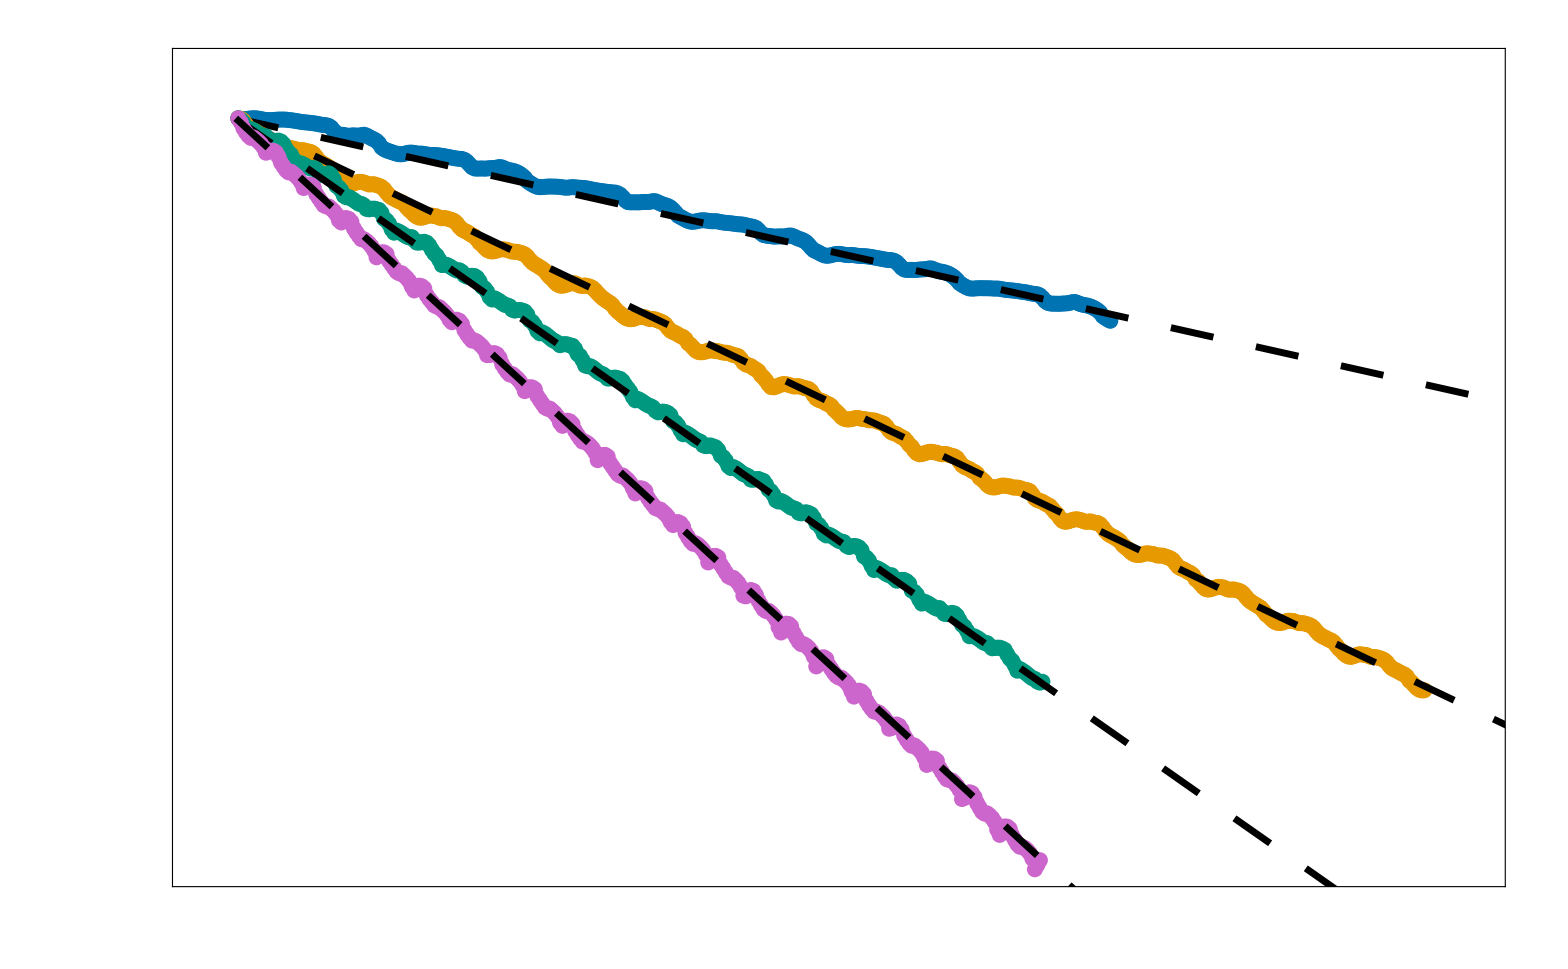

```mathematica
fig = Show[ListPlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_1Hz.csv"], PlotRange->{{-0.5, 16.5}, {-70, 5}}, PlotStyle->{AbsoluteThickness[8], RGBColor[0.0,0.45,0.7]},
Frame->True,
FrameStyle->Directive[Black, AbsoluteThickness[10]],
FrameTicks->{Table[{x, ,{0.01, 0}},{x,0,16,2}],Table[{y,, {0.01, 0}},{y,-70,5,10}]},FrameTicksStyle->Directive[Black, Bold,30],
ImageSize->1600
],
Plot[{-2Pi x (1/2)1/2}, {x, 0, 18}, PlotStyle->{{AbsoluteThickness[5],Dashing[{0.02,0.02}],Black}}], ListPlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_2Hz.csv"], PlotStyle->{AbsoluteThickness[8], RGBColor[0.9,0.6,0.0]}, PlotRange->All],
Plot[{-2Pi x (2/2)8/15}, {x, 0, 18}, PlotStyle->{{AbsoluteThickness[5],Dashing[{0.02,0.02}],Black}}], ListPlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_3Hz.csv"], PlotStyle->{AbsoluteThickness[8], RGBColor[0.0,0.6,0.5]}, PlotRange->All,PlotRange->{{0, 14}, {-70, 5}}],
Plot[{-2Pi x (3/2)12/23}, {x, 0, 18}, PlotStyle->{{AbsoluteThickness[5],Dashing[{0.02,0.02}],Black},{ Dashed, Purple}}], ListPlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_4Hz.csv"], PlotStyle->{AbsoluteThickness[8], RGBColor[0.8,0.4,0.8]}, PlotRange->All],
Plot[{-2Pi x (4/2)19/37}, {x, 0, 18}, PlotStyle->{{AbsoluteThickness[5],Dashing[{0.02,0.02}],Black}}]]
```

```mathematica
N[{1/2, 8/15, 12/23, 19/37}]
```

{0.5,0.533333,0.521739,0.513514}

```mathematica
Export["Fresh_spinning.svg",fig]
```

Fresh_spinning.svg

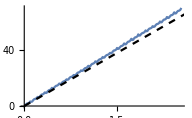

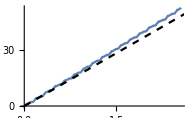

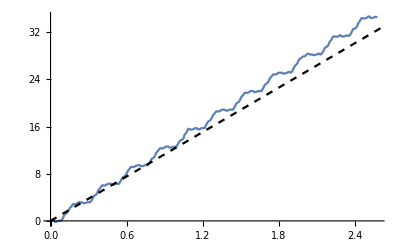
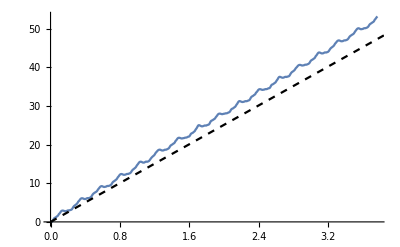
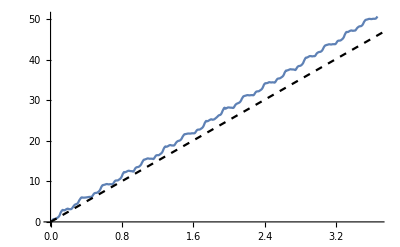
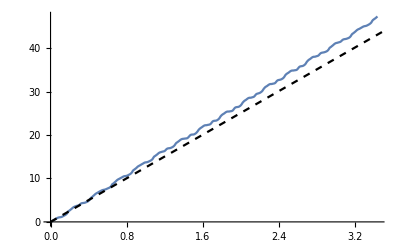

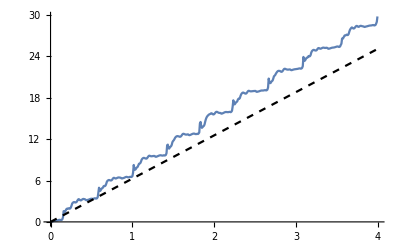
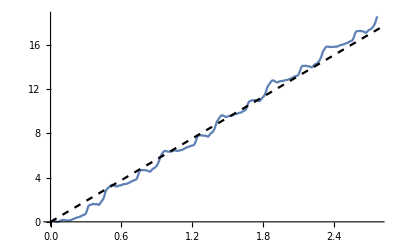

```mathematica
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_4hz.csv"][[;;-3]]],
Plot[{2Pi x (4/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_3hz.csv"][[;;-3]]],
Plot[{2Pi x (3/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
{Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_4cm_2hz.csv"][[;;-3]]],
Plot[{2Pi x (2/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]], Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_2hz.csv"][[;;-3]]],
Plot[{2Pi x (2/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]],Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_6cm_2hz.csv"][[;;-3]]],
Plot[{2Pi x (2/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]],Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_7cm_2hz.csv"][[;;-3]]],
Plot[{2Pi x (2/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]}
{Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_4cm_1hz.csv"][[;;-3]]],
Plot[{2Pi x (1/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]], Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_5cm_1hz.csv"][[;;-3]]],
Plot[{2Pi x (1/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]],Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_6cm_1hz.csv"][[;;-3]]],
Plot[{2Pi x (1/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]],Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_fresh\\Anglesnew_7cm_1hz.csv"][[;;-3]]],
Plot[{2Pi x (1/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]}
```